# Practica 1

## Objetivo:

Determinar teoricamente el comportamiento de la corriente en el resistor asi como la simulacion en software y corroborar los datos con los del circuito fisico empleando el osciloscopio.

Circuito RC

Simulacion en Multisim y Spice 
-Graphics--Graphics-

### Respuesta Forzada del Circuito RC

V+R i[t]+(∫i[t]ⅆt)/Ca==0

i[t]/Ca+R i'[t]==0

i[t]→(ⅇ^(-t/(Ca R)) V)/R

1/44 ⅇ^(-50000 t/11)

| Tiempo [s] | i(t) [A]
0 | 0. | 2.27273×10^-2
τ | 2.2×10^-4 | 8.3609×10^-3
2 τ | 4.4×10^-4 | 3.0758×10^-3
3 τ | 6.6×10^-4 | 1.13152×10^-3
4 τ | 8.8×10^-4 | 4.16265×10^-4
5 τ | 1.1×10^-3 | 1.53135×10^-4

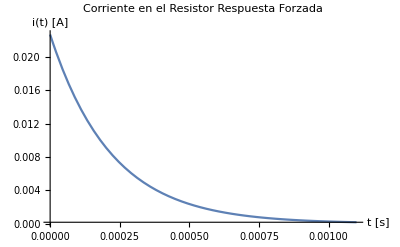

```mathematica
Vfv = 5; 
R1 = 220; 
C1 = 1/10^6; 
τ = R1*C1;
V + R*i[t] + (1/Ca)*Integrate[i[t], t] == 0
D[%, t]
DSolve[{%, i[0] == V/R}, {i[t]}, {t}]; 
Extract[%, {1, 1}]
i[t] /. %; 
% /. {Ca -> C1, R -> R1, V -> Vfv}
TableForm[Transpose[{Table[n*"τ", {n, 0, 5}], Table[ScientificForm[N[n*τ]], {n, 0, 5}], 
    Table[ScientificForm[N[% /. t -> n*τ]], {n, 0, 5}]}], 
  TableHeadings -> {None, {"", "Tiempo [s]", "i(t) [A]"}}]
Plot[%%, {t, 0, 5*τ}, PlotRange -> All, 
  PlotLabel -> "Corriente en el Resistor\n Respuesta Forzada", AxesLabel -> {"t [s]", "i(t) [A]"}]
```

### Respuesta Libre del Circuito RC

```mathematica
Vfv=5;
R1=220;
C1=1*10^(-6);
τ=R1*C1;
R i[t]+(1/Ca)*Integrate[i[t],t]==0
D[%,t]
DSolve[{%,i[0]==-V/R},{i[t]},{t}];
Extract[%,{1,1}]
i[t]/.%;
%/.{Ca->C1,R->R1,V->Vfv}
TableForm[Transpose[ {Table[n"τ",{n,0,5}],Table[ScientificForm[N[n*τ]],{n,0,5}],Table[ScientificForm[N[%/.t->(n*τ)]],{n,0,5}]}],TableHeadings->{None,{"","Tiempo [s]","i(t) [A]"}}]
Plot[%%,{t,0,5*τ},PlotLabel->"Corriente en el Resistor\n Respuesta Libre",  AxesLabel->{"t [s]","i(t) [A]"}]
```

R i[t]+(∫i[t]ⅆt)/Ca==0

i[t]/Ca+R i'[t]==0

i[t]→-(ⅇ^(-t/(Ca R)) V)/R

-1/44 ⅇ^(-50000 t/11)

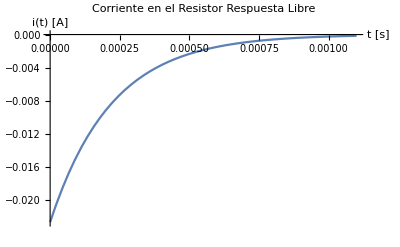

```mathematica
{{"", "Tiempo [s]", "i(t) [A]"}, {0, "0.", "-2.27273"×10^("-2")}, {"τ", "2.2"×10^("-4"), "-8.3609"×10^("-3")}, {2 "τ", "4.4"×10^("-4"), "-3.0758"×10^("-3")}, {3 "τ", "6.6"×10^("-4"), "-1.13152"×10^("-3")}, {4 "τ", "8.8"×10^("-4"), "-4.16265"×10^("-4")}, {5 "τ", "1.1"×10^("-3"), "-1.53135"×10^("-4")}}_□
```

### Las gráficas de la simulación en Multisim y Spice son las siguientes:

```mathematica
-Graphics--Graphics-
```

# Practica II

## Objetivo:

Determinar teoricamente el comportamiento de la corriente en el resistor asi como la simulacion en software y corroborar los datos con los del circuito fisico empleando el osciloscopio.

Circuito RL

Simulacion en Multisim y Spice 
-Graphics--Graphics-

#### Respuesta Libre del Circuito RL

R i[t]+L i'[t]==V

{{i[t]→(ⅇ^(-(R t)/L) (-1+ⅇ^((R t)/L)) V)/R}}

1/110 ⅇ^(-366.667 t) (-1+ⅇ^(366.667 t))

| Tiempo [s] | i(t) [A]
0 | 0. | 0.
τ | 2.72727×10^-3 | 5.74655×10^-3
2 τ | 5.45455×10^-3 | 7.86059×10^-3
3 τ | 8.18182×10^-3 | 8.6383×10^-3
4 τ | 1.09091×10^-2 | 8.9244×10^-3
5 τ | 1.36364×10^-2 | 9.02966×10^-3

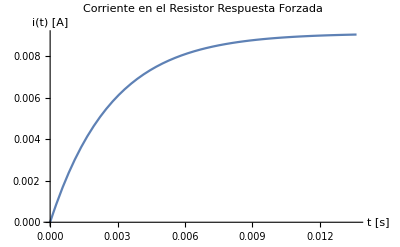

```mathematica
Vfv=5;
R1=220;
L1=1.5;
RL=330;
τL=L1/(R1+RL)//N;
R i[t]+(L)*D[i[t],t]==V
DSolve[{%,i[0]==0},{i[t]},{t}]
Extract[%,{1,1}];
i[t]/.%;
%/.{L->L1,R->R1+RL,V->Vfv}
TableForm[Transpose[ {Table[n"τ",{n,0,5}],Table[ScientificForm[N[n*τL]],{n,0,5}],Table[ScientificForm[%/.t->(n*τL)],{n,0,5}]}],TableHeadings->{None,{"","Tiempo [s]","i(t) [A]"}}]
Plot[%%,{t,0,5*τL},PlotRange->All,PlotLabel->"Corriente en el Resistor\n Respuesta Forzada",AxesLabel->{"t [s]","i(t) [A]"}]
5*τL
```

### Respuesta Libre del Circuito RL

R i[t]+L i'[t]==0

{{i[t]→(ⅇ^(-(R t)/L) V)/R}}

(ⅇ^(-(R t)/L) V)/R

ⅇ^(-366.667 t)/110

| Tiempo [s] | i(t) [A]
0 | 0. | 9.09091×10^-3
τ | 2.72727×10^-3 | 3.34436×10^-3
2 τ | 5.45455×10^-3 | 1.23032×10^-3
3 τ | 8.18182×10^-3 | 4.5261×10^-4
4 τ | 1.09091×10^-2 | 1.66506×10^-4
5 τ | 1.36364×10^-2 | 6.12541×10^-5

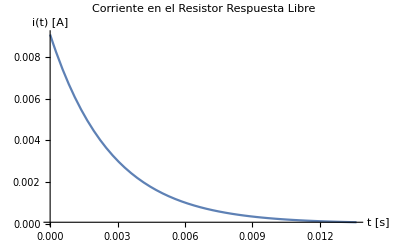

```mathematica
Vfv=5;
R1=220;
L1=1.5;
RL=330;
τL=L1/(R1+RL)//N;
R i[t]+(L)*D[i[t],t]==0
DSolve[{%,i[0]==V/R},{i[t]},{t}]
Extract[%,{1,1}];
i[t]/.%
%/.{L->L1,R->R1+RL,V->Vfv}
TableForm[Transpose[ {Table[n"τ",{n,0,5}],Table[ScientificForm[N[n*τL]],{n,0,5}],Table[ScientificForm[%/.t->(n*τL)],{n,0,5}]}],TableHeadings->{None,{"","Tiempo [s]","i(t) [A]"}}]
Plot[%%,{t,0,5*τL},PlotRange->All,PlotLabel->"Corriente en el Resistor\n Respuesta Libre", AxesLabel->{"t [s]","i(t) [A]"}]
```

### Las gráficas de la simulación en Multisim y Spice son las siguientes:

```mathematica
-Graphics-
-Graphics-
```